# QNM Package Testing

## Load from Kernel directory

```mathematica
QNMDir=ExpandFileName[FileNameJoin[{NotebookDirectory[],"..","Kernel","QNM.wl"}]];
Get[QNMDir];
```

## QNM frequencies from https://arxiv.org/pdf/2202.03837

```mathematica
data={{"(s,n,l,m)", "a", "Mω","_sΛ_l^m"},
{"(-2,0,2,2)","0","0.3736716 − 0.0889623ⅈ","4"},
{"(-2,0,2,2)","0.7","0.5326002 − 0.0807928ⅈ","2.9032 + 0.1832ⅈ"},
{"(-2,0,2,-2)","99/100","0.2921067 − 0.0880523ⅈ","4.7163 − 0.1966ⅈ"},
{"(-2,0,2,0)","99/100","0.4236846 − 0.0727008ⅈ", "3.9102 + 0.0319ⅈ"},
{"(-2,0,3,3)","99/100","1.3230831 − 0.029403ⅈ","6.4040 + 0.1043ⅈ"}};
```

```mathematica
dataTable=Grid[data,Frame->All,
ItemStyle->{Automatic,{Directive[Bold,FontSize->14]}},Background->{Automatic,{Lighter[Gray,0.9]}},Spacings->{1,1} ];
```

```mathematica
Labeled[dataTable,"Values from 2202.03837, Table 1",Top,LabelStyle->Directive[Bold, FontSize->16]]
```

(s,n,l,m) | a | Mω | _sΛ_l^m
(-2,0,2,2) | 0 | 0.3736716 − 0.0889623ⅈ | 4
(-2,0,2,2) | 0.7 | 0.5326002 − 0.0807928ⅈ | 2.9032 + 0.1832ⅈ
(-2,0,2,-2) | 99/100 | 0.2921067 − 0.0880523ⅈ | 4.7163 − 0.1966ⅈ
(-2,0,2,0) | 99/100 | 0.4236846 − 0.0727008ⅈ | 3.9102 + 0.0319ⅈ
(-2,0,3,3) | 99/100 | 1.3230831 − 0.029403ⅈ | 6.4040 + 0.1043ⅈValues from 2202.03837, Table 1

## Computed QNM frequencies

```mathematica
ClearAll[qnmdata,qnmvalues]
qnmdata = {{"(s,n,l,m)", "a", "Mω","_sΛ_l^m"}};
qnmvalues={{-2,2,2,0},{-2,2,2,0.7},{-2,2,-2,99/100},{-2,2,0,99/100},{-2,3,3,99/100}};
```

```mathematica
For[i=1,i<=Length[qnmvalues],i++,
args = StringJoin["(",StringRiffle[ToString/@qnmvalues[[i,1;;3]],","],")"];
λ = QNMFrequency@@qnmvalues[[i]];
AppendTo[qnmdata,{args,qnmvalues[[i]][[4]],NumberForm[λ["QNMfrequency"],{7,7}], NumberForm[λ["SeparationConstant"],{4,4}]}];
];
```

```mathematica
qnmTable=Grid[qnmdata,Frame->All,
ItemStyle->{Automatic,{Directive[Bold,FontSize->14]}},Background->{Automatic,{Lighter[Gray,0.9]}},Spacings->{1,1} ];
```

```mathematica
Labeled[qnmTable,"Calculated Values",Top,LabelStyle->Directive[Bold, FontSize->16]]
```

(s,n,l,m) | a | Mω | _sΛ_l^m
(-2,2,2) | 0 | 0.3736711-0.0889602 ⅈ | 4
(-2,2,2) | 0.7 | 0.5326009-0.0807926 ⅈ | 2.9030+0.1832 ⅈ
(-2,2,-2) | 99/100 | 0.2921073-0.0880523 ⅈ | 4.7160-0.1966 ⅈ
(-2,2,0) | 99/100 | 0.4236854-0.0727006 ⅈ | 3.9100+0.0319 ⅈ
(-2,3,3) | 99/100 | 0.9795426-0.1018119 ⅈ | 7.5490+0.3144 ⅈCalculated Values

## Radial QNM Profiles

```mathematica
result =QNMMode[-2,2,2,0.7,"Coordinates"->"Hyperboloidal"];
Subscript[ψ, s]=result["QNMRadialProfile"];
```

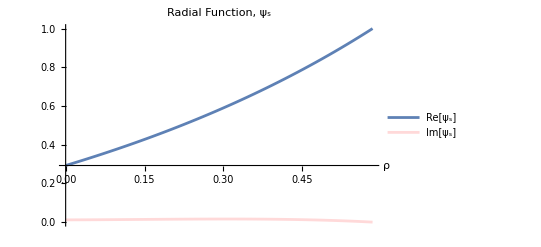

```mathematica
Show[Plot[Subscript[ψ, s][ρ]//Re,{ρ,Subscript[ψ, s]["Domain"]}//Flatten,PlotRange->All,PlotLegends->Placed[LineLegend[{"Re[ψ_s]"}],Automatic]],Plot[Subscript[ψ, s][ρ]//Im,{ρ,Subscript[ψ, s]["Domain"]}//Flatten,PlotStyle->LightRed,PlotRange->All,PlotLegends->Placed[LineLegend[{"Im[ψ_s]"}],Automatic]],
PlotLabel->"Radial Function, ψ_s",
LabelStyle->{FontSize->14},
AxesLabel->{"ρ"," "}]
```